Import Data

```mathematica
streckeTreppe = 9.39;
```

```mathematica
dataTreppeAb= SemanticImport["/home/dima/Dropbox/AAA_Studium/Master/Semester1/Modellbildung_und_Simulation/Gruppe/hm-modellbildung/angabe1/data/2017/Messungen_2017_Geschwindigkeit_Treppe_Ab.csv"]
```

Dataset[<>]

```mathematica
dataTreppeMitGeschw = dataTreppeAb[All,Append[#,"Geschwindigkeit"->streckeTreppe/#Zeit]&]
```

Dataset[<>]

## Histogramm

Es wird ein Histogramm erstellt und einer Normalverteilung gegenübergestellt. Für die Kurve der Normalverteilung muss der Erwartungswert und die Standardabweichung berechnet werden.

Berechnung des Mittelwertes und der Standardabweichung

```mathematica
geschwMean = Mean[dataTreppeMitGeschw[All, "Geschwindigkeit"]]
```

1.14729

```mathematica
geschwDeviation = StandardDeviation[dataTreppeMitGeschw[All, "Geschwindigkeit"]]
```

0.182581

Gegenüberstellung von Häufigkeitsverteilung und Normalverteilung. 
ACHTUNG: Das Histogramm wurde mit der Option “PDF” erstellt. Das bedeutet, dass nicht die absoluten Häufigkeiten sondern die Häufigkeitsdichte dargstellt ist, Damit lässt es sich besser mit dem Graphen der Normalverteilung vergleichen. Die Darstellung ist dann nicht mehr von der Anzahl der säulen abhängig.
Bemerkungen wie getrödelt wurden ignoriert. Es wird angenommen, dass im Schnitt es immer Personen gibt, die langsamer oder schneller gehen. Die Probanden hatten keine Vorgabe eine bestimmte Geschwindigkeit einzuhalten. Somit sind auch Probanden zu berücksichtigen, die langsamer oder schneller gehen. Es ist jedoch anzumerken, dass bei einem Versuch mit nur einer geringen Anzahl von Probanden, solche Sonderheiten eventuell eine signifikante Abweichung verursachen können.

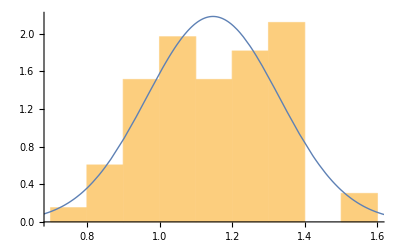

```mathematica
Show[Histogram[dataTreppeMitGeschw[All, "Geschwindigkeit"],10, "PDF"],Plot[PDF[NormalDistribution[geschwMean,geschwDeviation],x],{x,0,1.7},PlotStyle->Thick]]
```

## Quantileplot

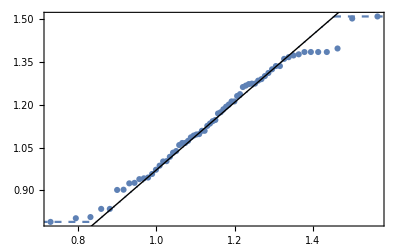

```mathematica
QuantilePlot[dataTreppeMitGeschw[All, "Geschwindigkeit"]]
```

## Distribution Fit Test

```mathematica
DistTestTreppe=DistributionFitTest[Array[dataTreppeMitGeschw[All, "Geschwindigkeit"], 66],Automatic,"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
DistTestTreppe["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 0.462731 | 0.259259
Baringhaus-Henze | 0.420106 | 0.209145
Cramér-von Mises | 0.0648248 | 0.333293
Jarque-Bera ALM | 2.23559 | 0.247476
Mardia Combined | 2.23559 | 0.247476
Mardia Kurtosis | -1.43247 | 0.152009
Mardia Skewness | 0.156589 | 0.692316
Pearson χ^2 | 10.6667 | 0.221311
Shapiro-Wilk | 0.974316 | 0.186898

Der Distribution Fit Test ergibt, dass die Geschwindigkeiten normalverteilt sind. Laut dem Cramer-von Mises Test wird die 5% Hürde überschritten.
Die Geschwindigkeiten Beim Runtergehen der Treppen sind normalverteilt. Die Ausreißer sind nicht periodisch und beeinflussen das Ergebnis nicht signifikant.

## Ausreißer entfernen

```mathematica
dataOhneAusreisser = dataTreppeMitGeschw[Select[#"Bemerkung"==""&], "Geschwindigkeit"]
```

Dataset[<>]

```mathematica
geschwNeuMean = Mean[dataOhneAusreisser]
```

1.15055

```mathematica
geschwNeuDeviation = StandardDeviation[dataOhneAusreisser]
```

0.17612

```mathematica
5
```

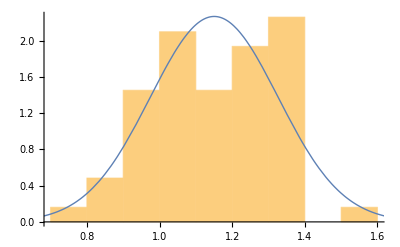

```mathematica
Show[Histogram[dataOhneAusreisser,10, "PDF"],Plot[PDF[NormalDistribution[geschwNeuMean,geschwNeuDeviation],x],{x,0,1.7},PlotStyle->Thick]]
```

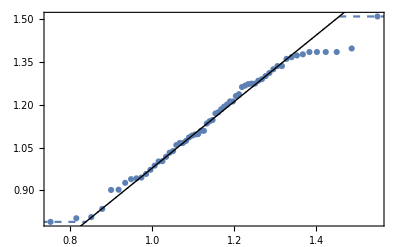

```mathematica
QuantilePlot[dataOhneAusreisser]
```

```mathematica
DistTestTreppeOhneAusreisser=DistributionFitTest[Array[dataOhneAusreisser, 54],Automatic,"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
DistTestTreppeOhneAusreisser["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 0.503916 | 0.205208
Baringhaus-Henze | 0.418485 | 0.187603
Cramér-von Mises | 0.0732779 | 0.256161
Jarque-Bera ALM | 1.99557 | 0.277317
Mardia Combined | 1.99557 | 0.277317
Mardia Kurtosis | -1.32774 | 0.184265
Mardia Skewness | 0.190686 | 0.662346
Pearson χ^2 | 3.40741 | 0.844933
Shapiro-Wilk | 0.969539 | 0.183952

Es ist festzustellen, dass die Geschwindigkeiten normalverteilt sind, wenn die Ausreißer nicht berücksichtigt werden. Für spätere betrachtung muss entschieden werden, ob diese Ausreisser in die Auswertung mit einfließen oder nicht. 
ACHTUNG: Der Distribution Fit Test fällt “schlechter” aus, wenn die Ausreisser entfernt werden.